```mathematica
(*_________________________________________________________________________________________________________________________________________________________________________________*)
(* Compiled-Single File-Equations *)
(* The calculations for the strain impact have been incorporated in the themodynamic variables already.  For calculations of the impact just from the polar expression(strain-free) or just from the strain, see File 1.1 Ferroelectric Bulk Crystal Code *)
Clear["`*"]
Clear["u1", "u2", "u3", "u4", "u5", "u6"];
Clear["a1", "a11","a12","a111","a112","a123","a1111","a1112","a1122","a1123"];
Clear["Q11", "Q12", "Q44", "A11", "A12", "Po"];
Symbol[ "a1"]Symbol[ "a11"]Symbol[ "a12"]Symbol[ "a111"]Symbol[ "a112"]Symbol[ "a123"]Symbol[ "a1111"]Symbol[ "a1112"]Symbol[ "a1122"]Symbol["a1123"];
Symbol["P1"] Symbol["P2"] Symbol["P3"]Symbol["u1"]Symbol[ "u2"]Symbol["u3"]Symbol["u4"]Symbol[ "u5"]Symbol[ "u6"];
Symbol["Q11"] Symbol["Q12"] Symbol["Q44"];
```

```mathematica
(*______________________________________________________________________________________________________________________________________________________________________________________________________________________________________________________________________________________________________________________________________________*)
(* TENSOR NOTATION *)
FPolar[P_]=Subscript[a,1](Sum[Subscript[P,i]^2, {i,1,3}])  +Subscript[a,11](Sum[Subscript[P,i]^4,{i,1,3}])+Subscript[a,12](Sum[Subscript[P,i]^2*Subscript[P,j]^2, {j,1,3}, {i,1,j-1}]) +
Subscript[a,111](Sum[Subscript[P,i]^6, {i,1,3}])+1/2*Simplify[Subscript[a,112](Sum[Subscript[P,i]^2*(Subscript[P,j]^4+Subscript[P,k]^4)(Boole[i≠j]&&Boole[i≠k]&&Boole[j≠k]),{i,1,3} ,{j,1,3}, {k,1,3}])]+Subscript[a,123](Sum[Subscript[P,i]^2Subscript[P,j]^2Subscript[P,k]^2, {i,1,3},{j,1,i-1},{k,1,j-1}])/.{False->0, True->1};
FPolarEighth[P_]=(Subscript[a,1](Sum[Subscript[P,i]^2, {i,1,3}])  +Subscript[a,11](Sum[Subscript[P,i]^4,{i,1,3}])+Subscript[a,12](Sum[Subscript[P,i]^2*Subscript[P,j]^2, {j,1,3}, {i,1,j-1}]) +Subscript[a,111](Sum[Subscript[P,i]^6, {i,1,3}])+1/2*Simplify[Subscript[a,112](Sum[Subscript[P,i]^2*(Subscript[P,j]^4+Subscript[P,k]^4)(Boole[i≠j]&&Boole[i≠k]&&Boole[j≠k]),{i,1,3} ,{j,1,3}, {k,1,3}])]+Subscript[a,123](Sum[Subscript[P,i]^2Subscript[P,j]^2Subscript[P,k]^2, {i,1,3},{j,1,i-1},{k,1,j-1}])/.{False->0, True->1})+
	Subscript[a, 1111](Subscript[P, 1]^8 +Subscript[P, 2]^8 +Subscript[P, 3]^8 ) +Subscript[a, 1112](Subscript[P, 1]^6 (Subscript[P, 2]^2 +Subscript[P, 3]^2)+Subscript[P, 2]^6 (Subscript[P, 1]^2 +Subscript[P, 3]^2)+Subscript[P, 3]^6 (Subscript[P, 1]^2 +Subscript[P, 2]^2))+Subscript[a, 1122](Subscript[P, 1]^4 Subscript[P, 2]^4 +Subscript[P, 2]^4 Subscript[P, 3]^4+Subscript[P, 1]^4 Subscript[P, 3]^4 ) +Subscript[a, 1123](Subscript[P, 1]^4 Subscript[P, 2]^2 Subscript[P, 3]^2+Subscript[P, 1]^2 Subscript[P, 2]^4 Subscript[P, 3]^2+Subscript[P, 1]^2 Subscript[P, 2]^2 Subscript[P, 3]^4)
FElectrostriction[P_,u_]=-Subscript[q,11]*Sum[Subscript[u,i,i]Subscript[P,i]^2, {i,1,3}]-1/2Simplify[Subscript[q,12]*Sum[Subscript[u,i,i](Subscript[P,j]^2+Subscript[P,k]^2)( Boole[i≠j]&&Boole[i≠k]&&Boole[j≠k]),{i,1,3},{j,1,3},{k,1,3}]]-Subscript[q,44]*Sum[Subscript[u,i,j]*Subscript[P,i]*Subscript[P,j],{j,1,3}, {i,1,j-1}]/.{False->0, True->1}/.{Subscript[u,1,1]-> Subscript[u,1],Subscript[u,2,2]-> Subscript[u,2],Subscript[u,3,3]-> Subscript[u,3],Subscript[u,2,3]-> Subscript[u,4],Subscript[u,1,3]-> Subscript[u,5],Subscript[u,1,2]-> Subscript[u,6]};
FElastic[u_]=1/2*Subscript[c,11]*Sum[Subscript[u,i,i]^2 ,{i,1,3}]+Subscript[c,12]*Sum[Subscript[u,i,i]*Subscript[u,j ,j], {j,1,3}, {i,1,j-1}]+1/2*Subscript[c,44]*Sum[Subscript[u,i,j]^2,{j,1,3},{i,1,j-1}]/.{Subscript[u,1,1]-> Subscript[u,1],Subscript[u,2,2]-> Subscript[u,2],Subscript[u,3,3]-> Subscript[u,3],Subscript[u,2,3]-> Subscript[u,4],Subscript[u,1,3]-> Subscript[u,5],Subscript[u,1,2]-> Subscript[u,6]};
FGradient[P_]=Subscript[g,11]/2*Sum[Subscript[P, i,i]^2, {i,1,3}]+Subscript[g,12]*Sum[Subscript[P,i,i]Subscript[P,j,j],{j,1,3},{i,1,j-1}]+Subscript[g,44]/2*Sum[(Subscript[P,i,j]+Subscript[P,j,i])^2, {j,1,3},{i,1,j-1}];
FBulk[P_,u_]=FPolar[P]+FElectrostriction[P, u]+FElastic[u](*+FGradient[P]; *);
```

a_123 P_1^2 P_2^2 P_3^2+a_1 (P_1^2+P_2^2+P_3^2)+a_12 (P_1^2 P_2^2+P_1^2 P_3^2+P_2^2 P_3^2)+a_11 (P_1^4+P_2^4+P_3^4)+a_1123 (P_1^4 P_2^2 P_3^2+P_1^2 P_2^4 P_3^2+P_1^2 P_2^2 P_3^4)+a_1122 (P_1^4 P_2^4+P_1^4 P_3^4+P_2^4 P_3^4)+a_111 (P_1^6+P_2^6+P_3^6)+a_1111 (P_1^8+P_2^8+P_3^8)+a_1112 ((P_1^2+P_2^2) P_3^6+P_2^6 (P_1^2+P_3^2)+P_1^6 (P_2^2+P_3^2))+a_112 (P_1^4 (P_2^2+P_3^2)+P_2^2 P_3^2 (P_2^2+P_3^2)+P_1^2 (P_2^4+P_3^4))

```mathematica
(*__________________________________________________________________________________________________________________________________________________________________*)
(* New Rules Functions to take Derivatives of subscripted notations. *)
SubToVariableRules={Subscript[P, 1,1]-> PG11,Subscript[P, 1,2]-> PG12, Subscript[P, 1,3]-> PG13, Subscript[P, 2,2]-> PG22, Subscript[P, 2,1]-> PG21, Subscript[P, 3,1]-> PG31, Subscript[P, 2,3]-> PG23, Subscript[P, 3,2]-> PG32, Subscript[P, 3,3]-> PG33,Subscript[P, 1] -> P1, Subscript[P, 2] -> P2,Subscript[P, 3] -> P3,
	Subscript[u, 1]-> u1,Subscript[u, 2]-> u2,Subscript[u, 3]-> u3,Subscript[u, 4]-> u4,Subscript[u, 5]-> u5,Subscript[u, 6]-> u6};
VariableToSubRules={ PG11-> Subscript[P, 1,1],PG12-> Subscript[P, 1,2],PG13-> Subscript[P, 1,3],PG22-> Subscript[P, 2,2],PG21-> Subscript[P, 2,1],PG31-> Subscript[P, 3,1],PG23-> Subscript[P, 2,3],PG32-> Subscript[P, 3,2],PG33-> Subscript[P, 3,3],P1-> Subscript[P, 1],P2-> Subscript[P, 2],P3-> Subscript[P, 3],
	u1-> Subscript[u, 1],u2-> Subscript[u, 2],u3-> Subscript[u, 3],u4-> Subscript[u, 4],u5-> Subscript[u, 5],u6-> Subscript[u, 6]};
CoefficientsToVariables={Subscript[a, 1]->a1,Subscript[a, 11]->a11, Subscript[a, 12]->a12,Subscript[a, 111]->a111,Subscript[a, 112]->a112,Subscript[a, 123]->a123,
	Subscript[a, 1111]->a1111,Subscript[a, 1112]->a1112,Subscript[a, 1122]->a1122,Subscript[a, 1123]->a1123,
	Subscript[c, 11]->c11,Subscript[c, 12]->c12,Subscript[c, 44]->c44,Subscript[q, 11]->q11,Subscript[q, 12]->q12,Subscript[q, 44]->q44};
(* Thermodynamic Coefficients and Elastic Constants *)
WangCoefficients={ a1->3.61*(10^5)*(T-391),a11->(-1.83*(10^9)+4*(10^6)*T),a12->-2.24*10^9+6.7*(10^6)*T,a111->(1.39*10^10-3.2*10^7*T),a112->-2.2*10^9,a123->5.51*10^10,a1111->4.84*(10^10),a1112->2.53*10^11,a1122->2.80*10^11,a1123->9.35*10^10, Q11->14.20*10^9,Q12->-0.74*10^9,Q44->1.57*10^9};
	       (* TElasticConstants={c11-> 300*10^9,c12->109*10^9};            OElasticConstants={c11->150*10^9,c22->312*10^9,c33->150*10^9,c44->135*10^9,c12->100*10^9}; *)
LiCoefficients={a1->4.124*10^5*(T-388),a11->-2.097*10^8,a12->7.974*10^8,a111->1.294*10^9,a112->-1.95*10^9,a123->-2.5*10^9,
	a1111->3.863*10^10,a1112->2.529*10^10,a1122->1.637*10^10,a1123->1.367*10^10,c11->27.50*10^10,c12->17.90*10^10,c44->5.43*10^10, 
	q11->14.20*10^9,q12->-0.74*10^9,q44->1.57*10^9};
BellCoefficients={a1->3.34*10^5*(T-381),a11->4.69*10^6*(T-393)-2.02*10^8,a12->-3.23*10^8,a111->-5.52*10^7*(T-393)+2.76*10^9,a112->4.47*10^9,
	a123->4.91*10^9, a1111->3.863*10^10,c11->27.50*10^10,c12->17.90*10^10,c44->5.43*10^10, q11->14.20*10^9,q12->-0.74*10^9,q44->1.57*10^9};
```

```mathematica
(*______________________________________________________________________________________________________________________________________________*)
(* Determining the Equilibrium Solutions for the Polarization vector for Each Phase  *)
(*Tetragonal Case *)
D[FPolar[P]/.SubToVariableRules, P3]/.P1->0/.P2->0/.CoefficientsToVariables;
TetragonalBC={P1->0,P2->0};
(* The Deriviative of the free energy is simplified even further to solve for the square of the polarization for an eighth order free energy in order to reduce the number of extracted solutions from the first derivative. *)
TSolutionsForP8=Simplify[Solve[Simplify[(D[FPolarEighth[P]/.SubToVariableRules,P3]/.TetragonalBC)==0, P3≠0]/.P3-> P3^(1/2), P3]];
TSolutionsForP=Simplify[Solve[0==D[FPolar[P]/.SubToVariableRules, P3]/.TetragonalBC, P3]];
Plot[{Sqrt[P3/.TSolutionsForP8[[1]]//.CoefficientsToVariables/.WangCoefficients],
	Sqrt[P3/.TSolutionsForP8[[2]]//.CoefficientsToVariables/.WangCoefficients],
	Sqrt[P3/.TSolutionsForP8[[3]]//.CoefficientsToVariables/.WangCoefficients]},{T,260,400}];
(* Solutions for Eighth and Sixth order expansions of Phi *)
PTetragonalEighth=Sqrt[P3/.TSolutionsForP8[[1]]];
PTetragonal=√((-Subscript[a, 11]+√(Subscript[a, 11]^2-3 Subscript[a, 1] Subscript[a, 111]))/(3 Subscript[a, 111]));
LegendPT=LineLegend[{Blue,Green,Red, Directive[Black,Dashed]},{"Wang et al.", "Bell and Cross", "Li et al.","T_C (Curie Temperature)"}];
GraphicsGrid[{{
Show[Plot[PTetragonalEighth//.CoefficientsToVariables/.WangCoefficients, {T, 260,403}, ColorFunction->Function[T,Blue]],
	Plot[PTetragonal//.CoefficientsToVariables/.BellCoefficients,  {T, 260,392},ColorFunction->Function[T,Green]],
	Plot[PTetragonalEighth//.CoefficientsToVariables/.LiCoefficients, {T, 260,398}, ColorFunction->Function[T,Red]],
	Epilog->{Dashed,{Blue,Line[{{403,0},{403,Re[PTetragonalEighth//.CoefficientsToVariables/.WangCoefficients/.T-> 403]}}]},
				{Red,Line[{{398,0},{398,Re[PTetragonalEighth//.CoefficientsToVariables/.LiCoefficients/.T-> 398]}}]},
				{Green,Line[{{392,0},{392,Re[PTetragonal//.CoefficientsToVariables/.BellCoefficients/.T-> 392]}}]}},
	AxesLabel->{"Temperature[°K]","Polarization (C/m^2)"},AxesOrigin-> {280,0.1},PlotRange-> {{280,405},{0.1,0.3}}, PlotLabel-> "Spontaneous Polarization for the Tetragonal Phase"], LegendPT}}];
(* For the Orthorhombic Phase *)
P=.
OrthorhombicBC={P1->P/Sqrt[2],P3-> P/Sqrt[2],P2-> 0};
FPolarizationDerivative[P_]=MatrixForm[Collect[Simplify[D[FPolar[P]/.SubToVariableRules, {{P1,P2,P3}}]]/.OrthorhombicBC, P]];

OSolutionsForP=Solve[Simplify[(D[FPolar[P]/.SubToVariableRules,P3]/.OrthorhombicBC)==0], P];
OSolutionsForP8=Solve[Simplify[(D[FPolarEighth[P]/.SubToVariableRules,P3]/.OrthorhombicBC)==0, P≠0]/.P-> P^(1/2), P];

Plot[{Sqrt[P/.OSolutionsForP8[[1]]//.CoefficientsToVariables/.WangCoefficients],
	Sqrt[P/.OSolutionsForP8[[2]]//.CoefficientsToVariables/.WangCoefficients],
	Sqrt[P/.OSolutionsForP8[[3]]//.CoefficientsToVariables/.WangCoefficients]},{T,200,400}];
POrthorhombicEighth=Sqrt[P/.OSolutionsForP8[[1]]];
POrthorhombic=√(-(2 Subscript[a, 11])/(3 (Subscript[a, 111]+Subscript[a, 112]))-Subscript[a, 12]/(3 (Subscript[a, 111]+Subscript[a, 112]))+(√((4 Subscript[a, 11]+2 Subscript[a, 12])^2-16 Subscript[a, 1] (3 Subscript[a, 111]+3 Subscript[a, 112])))/(6 (Subscript[a, 111]+Subscript[a, 112])));

Plot[{POrthorhombicEighth/.CoefficientsToVariables/.WangCoefficients,
	POrthorhombic/.CoefficientsToVariables/.BellCoefficients,
	 POrthorhombicEighth/.CoefficientsToVariables/.LiCoefficients},{T, 200,400},AxesLabel->{"Temperature[°K]","Polarization (C/m^2)"}, PlotLabel-> "Spontaneous Polarization for the Orthorhombic Phase", PlotLegends-> {"Wang et al.", "Bell and Cross", "Li et al."}];
```

```mathematica
(* Combined Plots for all three coefficient sets *)
LegendCTO=LineLegend[{Blue,Green,Red, Directive[Black,Dashed]},{"Wang et al.", "Bell and Cross", "Li et al.","T_Tr (Transition Temperatures)"}];
GraphicsGrid[{{
Show[Plot[PTetragonalEighth//.CoefficientsToVariables/.WangCoefficients, {T, 285,403}, ColorFunction->Function[T,Blue]],
	Plot[PTetragonal//.CoefficientsToVariables/.BellCoefficients,  {T, 283,392},ColorFunction->Function[T,Green]],
	Plot[PTetragonalEighth//.CoefficientsToVariables/.LiCoefficients, {T, 281,398}, ColorFunction->Function[T,Red]],
	Plot[POrthorhombicEighth//.CoefficientsToVariables/.WangCoefficients, {T, 220,285}, ColorFunction->Function[T,Blue]],
	Plot[POrthorhombic//.CoefficientsToVariables/.BellCoefficients,  {T, 220,283},ColorFunction->Function[T,Green]],
	Plot[POrthorhombicEighth//.CoefficientsToVariables/.LiCoefficients, {T, 220,281}, ColorFunction->Function[T,Red]],Epilog->{Dashed,{Blue,Line[{{403,0},{403,Re[PTetragonalEighth//.CoefficientsToVariables/.WangCoefficients/.T-> 403]}}]},
{Blue,Line[{{285,Re[PTetragonalEighth//.CoefficientsToVariables/.LiCoefficients/.T-> 285]},{285,Re[POrthorhombicEighth//.CoefficientsToVariables/.WangCoefficients/.T-> 285]}}]},
{Red,Line[{{398,0},{398,Re[PTetragonalEighth//.CoefficientsToVariables/.LiCoefficients/.T-> 398]}}]},
{Red,Line[{{281,Re[PTetragonalEighth//.CoefficientsToVariables/.LiCoefficients/.T-> 281]},{281,Re[POrthorhombicEighth//.CoefficientsToVariables/.LiCoefficients/.T-> 281]}}]},
{Green,Line[{{392,0},{392,Re[PTetragonal//.CoefficientsToVariables/.BellCoefficients/.T-> 392]}}]},
{Green,Line[{{283,Re[PTetragonalEighth//.CoefficientsToVariables/.LiCoefficients/.T-> 283]},{283,Re[POrthorhombic//.CoefficientsToVariables/.BellCoefficients/.T-> 283]}}]}},
	AxesLabel->{"Temperature[°K]","Polarization (C/m^2)"},AxesOrigin-> {220,0.1},PlotRange-> {{220,405},{0.1,0.37}}, PlotLabel-> "Spontaneous Polarization (Magnitude) for Barium Titanate"], LegendCTO}}];
GraphicsGrid[{{
Show[Plot[PTetragonalEighth//.CoefficientsToVariables/.WangCoefficients, {T, 285,403}, ColorFunction->Function[T,Blue]],
	Plot[PTetragonal//.CoefficientsToVariables/.BellCoefficients,  {T, 283,392},ColorFunction->Function[T,Green]],
	Plot[PTetragonalEighth//.CoefficientsToVariables/.LiCoefficients, {T, 281,398}, ColorFunction->Function[T,Red]],
	Plot[POrthorhombicEighth/Sqrt[2]//.CoefficientsToVariables/.WangCoefficients, {T, 220,285}, ColorFunction->Function[T,Blue]],
	Plot[POrthorhombic/Sqrt[2]//.CoefficientsToVariables/.BellCoefficients,  {T, 220,283},ColorFunction->Function[T,Green]],
	Plot[POrthorhombicEighth/Sqrt[2]//.CoefficientsToVariables/.LiCoefficients, {T, 220,281}, ColorFunction->Function[T,Red]],Epilog->{Dashed,{Blue,Line[{{403,0},{403,Re[PTetragonalEighth//.CoefficientsToVariables/.WangCoefficients/.T-> 403]}}]},
{Blue,Line[{{285,Re[PTetragonalEighth//.CoefficientsToVariables/.LiCoefficients/.T-> 285]},{285,Re[POrthorhombicEighth/Sqrt[2]//.CoefficientsToVariables/.WangCoefficients/.T-> 285]}}]},
{Red,Line[{{398,0},{398,Re[PTetragonalEighth//.CoefficientsToVariables/.LiCoefficients/.T-> 398]}}]},
{Red,Line[{{281,Re[PTetragonalEighth//.CoefficientsToVariables/.LiCoefficients/.T-> 281]},{281,Re[POrthorhombicEighth/Sqrt[2]//.CoefficientsToVariables/.LiCoefficients/.T-> 281]}}]},
{Green,Line[{{392,0},{392,Re[PTetragonal//.CoefficientsToVariables/.BellCoefficients/.T-> 392]}}]},
{Green,Line[{{283,Re[PTetragonalEighth//.CoefficientsToVariables/.LiCoefficients/.T-> 283]},{283,Re[POrthorhombic/Sqrt[2]//.CoefficientsToVariables/.BellCoefficients/.T-> 283]}}]}},
	AxesLabel->{"Temperature[°K]","Polarization (C/m^2)"},AxesOrigin-> {220,0.1},PlotRange-> {{220,405},{0.1,0.30}}, PlotLabel-> "Spontaneous Polarization (Components) for Barium Titanate"], LegendCTO}}];
```

```mathematica
(* For the Monoclinic Phase *)
(*
MonoclinicBC={P2-> 0};
PMcSolutions=Drop[Solve[{Simplify[(D[FPolarEighth[P]/.SubToVariableRules,P1]/.MonoclinicBC)==0, {P1≠0, P3≠0}],
				Simplify[(D[FPolarEighth[P]/.SubToVariableRules,P3]/.MonoclinicBC)==0, {P1≠0, P3≠0}],P1≠0,P3≠0, P1≠P3} , {P1,P3}]/.VariableToSubRules,-4];
(* The final four solutions coincide with the Orthorhombic symmetry *)
P1Monoclinic=1/(√2)(√(1/(-3 Subscript[a, 111]+Subscript[a, 112])^2(C+√(3 Subscript[a, 111]-Subscript[a, 112]) √(-36 Subscript[a, 1] Subscript[a, 111]^2-Subscript[a, 112] (20 A11^2-12 A11 A12+A12^2+4 Subscript[a, 1] Subscript[a, 112])+3 Subscript[a, 111] (4 A11^2+4 A11 A12-3 A12^2+8 Subscript[a, 1] Subscript[a, 112])))))/.C-> ((-6 A11+3 A12) Subscript[a, 111]+2 A11 Subscript[a, 112]-A12 Subscript[a, 112]);
P3Monoclinic=1/(√(6 Subscript[a, 111]-2 Subscript[a, 112]))(√(1/(3 Subscript[a, 111]-Subscript[a, 112])(C+√(3 Subscript[a, 111]-Subscript[a, 112]) √(-36 Subscript[a, 1] Subscript[a, 111]^2-Subscript[a, 112] (20 A11^2-12 A11 A12+A12^2+4 Subscript[a, 1] Subscript[a, 112])+3 Subscript[a, 111] (4 A11^2+4 A11 A12-3 A12^2+8 Subscript[a, 1] Subscript[a, 112])))))/.C-> ((-6 A11+3 A12) Subscript[a, 111]+2 A11 Subscript[a, 112]-A12 Subscript[a, 112]);
*)
(* Determining the real conditions of the polarization solutions for each phase
Simplify[(PTSolutions//.CoefficientsToVariables/.ThermodynamicCoefficients/.T-> 373)]
Simplify[POSolutions//.CoefficientsToVariables/.ThermodynamicCoefficients/.T-> 283]
Simplify[PMcSolutions//.CoefficientsToVariables/.ThermodynamicCoefficients/.T-> 283] *)
```

```mathematica
(*___________________________________________________________________________________________________________________________________________________________________________________*)
(* Inserting the polarization solutions into the free energy for each respective phase determines the most stable phase (i.e. the phase with the lowest free energy) *)
(* For the Cubic Phase *)
FCubic=FPolarEighth[P]/.SubToVariableRules/.{P1->0,P2->0,P3->0};
(* For the Tetragonal Phase *)
FTetragonalSixth=Simplify[(FPolar[P])/.SubToVariableRules]/.{P1->0,P2->0,P3->PTetragonal};
FTetragonal=Simplify[(FPolarEighth[P])/.SubToVariableRules]/.{P1->0,P2->0,P3->PTetragonalEighth};
(* For the Orthorhombic Phase *)
FOrthorhombicSixth=Simplify[(FPolar[P])/.SubToVariableRules]/.{P1->POrthorhombic/2^(1/2),P2->0,P3->POrthorhombic/2^(1/2)};
FOrthorhombic=Simplify[(FPolarEighth[P])/.SubToVariableRules]/.{P1->POrthorhombicEighth/2^(1/2),P2->0,P3->POrthorhombicEighth/2^(1/2)};
(* C-T Phase Transition Temperature for each Coefficient set *)
(* Numerical Evaluation -(Long Script Time *)
(* Print[{ "Li C-T Temp." Solve[((FTetragonal-FCubic)/.CoefficientsToVariables/.LiCoefficients)==0, T],
	    "Bell C-T Temp." Solve[((FTetragonal-FCubic)/.CoefficientsToVariables/.BellCoefficients)==0, T],
	    "Wang C-T Temp." Solve[((FTetragonal-FCubic)/.CoefficientsToVariables/.WangCoefficients)==0, T]}]
(* The Tetragonal-Orthorhombic Transition Temperature for each Coefficient set *)
Print[{"Li T-O Temp." Solve[((FTetragonal-FOrthorhombic)/.CoefficientsToVariables/.LiCoefficients)==0, T],
	  "Bell T-O Temp." Solve[((FTetragonal-FOrthorhombicSixth)/.CoefficientsToVariables/.BellCoefficients)==0, T],
	  "Wang T-O Temp." Solve[((FTetragonal-FOrthorhombic)/.CoefficientsToVariables/.WangCoefficients)==0, T]}] *)

(* Graphical Evaluation -(B&C give a high Transition temp. for C-T and T-O Phases *)
Plot[{FTetragonal/.CoefficientsToVariables/.LiCoefficients, FTetragonalSixth/.CoefficientsToVariables/.BellCoefficients, FTetragonal/.CoefficientsToVariables/.WangCoefficients}, 
			{T, 385,407}, PlotLegends->{"Li et al.", "Bell and Cross", "Wang et al."}];
(*Li-398 Kelvin, Bell and Cross-392 Kelvin, Wang-403 Kelvin *)
Plot[{FTetragonal/.CoefficientsToVariables/.LiCoefficients,FOrthorhombic/.CoefficientsToVariables/.LiCoefficients}, {T,278,284}, PlotLabel->"Li et al."];
Plot[{FTetragonalSixth/.CoefficientsToVariables/.BellCoefficients,FOrthorhombicSixth/.CoefficientsToVariables/.BellCoefficients}, {T,250,400}, PlotLabel->"Bell and Cross"];
Plot[{FTetragonal/.CoefficientsToVariables/.WangCoefficients, FOrthorhombic/.CoefficientsToVariables/.WangCoefficients}, {T,282,288}, PlotLabel->"Wang et al."];
(* Li-281 Kelvin, Bell and Cross-   Kelvin, Wang-285 Kelvin *)

(* For the Monoclinic Phase *)
(* FMonoclinic=Simplify[(FPolarEighth[P]-FGradient[P])/.SubToVariableRules]/.
{P1->P1Monoclinic,P2->0,P3->P3Monoclinic}/.VariableToSubRules;
FinalFreeEnergies={Simplify[(FTetragonal//.CoefficientsToVariables/.LiCoefficients)],
Simplify[(FOrthorhombic//.CoefficientsToVariables/.LiCoefficients)],
Simplify[(FMonoclinic//.CoefficientsToVariables/.LiCoefficients)]}; *)
```

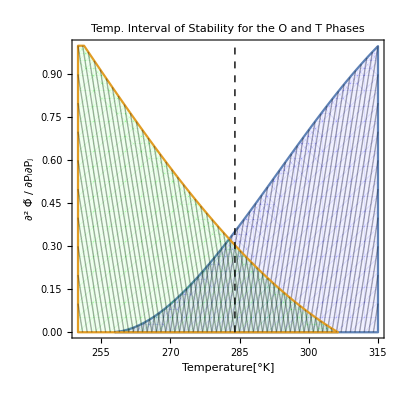

```mathematica
(*---------------------------------------------------------------------------------------------------------------------------------------------------------------------------*)
(*---------------------------------------------------------------------------------------------------------------------------------------------------------------------------*)
(* Entry 2/10/16 Renormalizing the Free Energy Second Derivative to have a neater figure for journal articles showing the overlap of stability *)
(* Renormalizing the free energy *)
TFreeEnergy=FPolar[P]/.SubToVariableRules/.TetragonalBC;
TFreeEnergy/(4.124*10^5*(388))/.P3->PTetragonal/.CoefficientsToVariables/.LiCoefficients;
Plot[TFreeEnergy/(4.124*10^5*(388))/.P3->PTetragonal//.CoefficientsToVariables/.LiCoefficients, {T, 0,2}];
(* Solving the second derivative of the free energy for each phase *)
P=.;
CStability=Simplify[Det[D[FPolar[P]/.SubToVariableRules, {{P1,P2,P3},2}]/.TetragonalBC/.P3->0]≥0];
TStability=Simplify[Det[D[FPolar[P]/.SubToVariableRules, {{P1,P2,P3},2}]/.TetragonalBC/.P3->PTetragonal]];
OStability=Simplify[Det[D[FPolar[P]/.SubToVariableRules, {{P1,P2,P3},2}]/.OrthorhombicBC//.P-> POrthorhombic]];

MatrixForm[(D[FPolarEighth[P]/.SubToVariableRules, {{P1,P2,P3},2}]/.TetragonalBC)*{{1,0,0},{0,1,0},{0,0,1}}];

TStabilityEighth=Det[D[FPolarEighth[P]/.SubToVariableRules, {{P1,P2,P3},2}]/.TetragonalBC]/.P3->PTetragonalEighth;
OStabilityEighth=Det[D[FPolarEighth[P]/.SubToVariableRules, {{P1,P2,P3},2}]/.OrthorhombicBC]/.P-> POrthorhombicEighth;

LegendOT=LineLegend[{Blue,Green,Directive[Black, Dashed]},{"Tetragonal Stability Range","Orthorhombic Stability Range","T_Tr (Transition Temperature)"}];
(* Plot[TStabilityEighth/.CoefficientsToVariables/.WangCoefficients,{T,250,320}, AxesOrigin->{250,0},PlotPoints->1000]
  Plot[OStabilityEighth/.CoefficientsToVariables/.WangCoefficients,{T,250,320}, AxesOrigin->{250,0}] *)
GraphicsGrid[{{
Show[
	RegionPlot[{Re[(TStabilityEighth/.CoefficientsToVariables/.WangCoefficients)]/(1.72*10^24)≥    y,-10==y}, {T,258,315},{y,0,1},
	MeshFunctions-> {#1-(#2*10)&}, Mesh-> {Range[258,315,1]}, PlotStyle->Directive[Blue,Opacity[0.06]]],
	RegionPlot[{-10==y,Re[(OStabilityEighth/.CoefficientsToVariables/.WangCoefficients)]/(8.8*10^24)≥  y}, {T,250,315},{y,0,1},
	MeshFunctions->{#1+(#2*10)&}, Mesh-> {Range[250,315,1]}, PlotStyle->Directive[Green, Opacity[0.06]]],
Epilog->{Dashed,Line[{{284,0},{284,1}}]},PlotRange-> {{250,315},{0,1}},AxesOrigin-> {250.0,0.0},
	FrameLabel->{"Temperature[°K]","∂^2 Φ̃ / ∂P_i∂P_j" }, PlotLabel-> "Temp. Interval of Stability for the O and T Phases"], LegendOT}}]
```

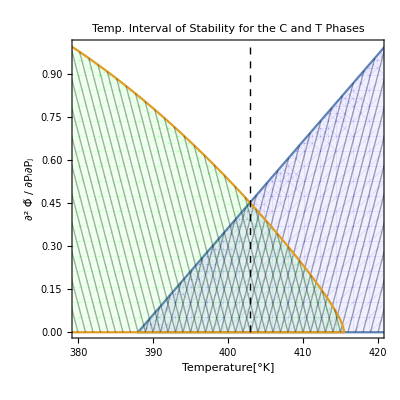

```mathematica
Symbol["y"];

(* The SHOW Function can combine different graphics; however, the legend component in any form is tempermental and will give errors *)
(* The Original graph in Degrees Kelvin *)
LegendCT=LineLegend[{Blue,Green,Directive[Black, Dashed]},{"Cubic Stability Range","Tetragonal Stability Range","T_C (Curie Temperature)"}];

(* Show[
Plot[{(a1/.LiCoefficients)/(1.31968*10^7), (TStability/.CoefficientsToVariables/.LiCoefficients)/(3.46523*10^24),0*T},{T,388,403},
		Epilog->{Dashed,Line[{{403,0},{403,1}}]},Filling-> {1-> Axis},FillingStyle-> Opacity[0.2,Blue]],
Plot[{(a1/.LiCoefficients)/(1.31968*10^7), (TStability/.CoefficientsToVariables/.LiCoefficients)/(3.46523*10^24),0*T},{T,403,420},
	   Epilog->{Dashed,Line[{{403,0},{403,1}}]}, Filling-> {2-> Axis}, FillingStyle-> Opacity[0.4,Green],PlotRange->{0,1}],
PlotRange-> {{385,420},{0.00,1}},AxesOrigin-> {385.0,0.0},AxesLabel->{"Temperature[°K]","∂^2 Φ̃/∂P_i∂P_j" }, 
PlotLabel-> "Temperature Interval of Stability for the Cubic and Tetragonal Phases"];

Show[
Plot[{(a1/.LiCoefficients)/(1.31968*10^7), (TStabilityEighth/.CoefficientsToVariables/.LiCoefficients)/(4.34*10^23),0*T},{T,388,403},
		Epilog->{Dashed,Line[{{403,0},{403,1}}]},Filling-> {1-> Axis},FillingStyle-> Opacity[0.2,Blue]],
Plot[{(a1/.LiCoefficients)/(1.31968*10^7), (TStabilityEighth/.CoefficientsToVariables/.LiCoefficients)/(4.34*10^23),0*T},{T,403,420},
	   Epilog->{Dashed,Line[{{403,0},{403,1}}]}, Filling-> {2-> Axis}, FillingStyle-> Opacity[0.4,Green],PlotRange->{0,1}],
PlotRange-> {{385,420},{0.00,1}},AxesOrigin-> {385.0,0.0},AxesLabel->{"Temperature[°K]","∂^2 Φ̃/∂P_i∂P_j" }, 
PlotLabel-> "Temperature Interval of Stability for the Cubic and Tetragonal Phases"]; *)

                                    (*    Region Plot in Kelvin *)
GraphicsGrid[{{
Show[
RegionPlot[{(a1/.LiCoefficients)/(1.361*10^7)≥    y,-10==y}, {T,380,421},{y,0,1},
MeshFunctions-> {#1-(#2*10)&}, Mesh-> {Range[388,420,1]}, PlotStyle->Directive[Blue,Opacity[0.06]]],
RegionPlot[{-10==y,Re[(TStability/.CoefficientsToVariables/.LiCoefficients)]/(3.527*10^24)≥  y}, {T,375,425},{y,0,1}, 
MeshFunctions->{#1+(#2*10)&}, Mesh-> {Range[380,416,1]}, PlotStyle->Directive[Green, Opacity[0.06]]],
Epilog->{Dashed,Line[{{403,0},{403,1}}]},PlotRange-> {{380,420},{0,1}},AxesOrigin-> {381.0,0.0},
FrameLabel->{"Temperature[°K]","∂^2 Φ̃ / ∂P_i∂P_j" }, PlotLabel-> "Temp. Interval of Stability for the C and T Phases"], LegendCT}}]
```

```mathematica
(* _______________________________________________________________________________________________________________________________ *)
(* In Degrees Celsius *)
(* CelsiusConversion={T-> (T+273)};
Show[
Plot[{(a1/.CelsiusConversion)/(1.15*10^7), (TStability/.CoefficientsToVariables/.LiCoefficients/.CelsiusConversion)/(2.913*10^24),0*T},{T,115,130},
		Epilog->{Dashed,Line[{{130,0},{130,1}}]}, Filling-> {1-> Axis},FillingStyle-> Opacity[0.2,Blue]],
Plot[{(a1/.CelsiusConversion)/(1.15*10^7), (TStability/.CoefficientsToVariables/.LiCoefficients/.CelsiusConversion)/(2.913*10^24),0*T},{T,130,143},
	   Epilog->{Dashed,Line[{{130,0},{130,1}}]}, Filling-> {2-> Axis}, FillingStyle-> Opacity[0.4,Green],PlotRange->{0,1}],
PlotRange-> {{110,145},{0.00,1}},AxesOrigin-> {110.0,0.0},AxesLabel->{"Temperature[°C]","∂^2 Φ̃/∂P_i∂P_j" }, 
PlotLabel-> "Temperature Interval of Stability for the Cubic and Tetragonal Phases"]

(*                                            Region Plot in Celsius            *)
Show[
RegionPlot[{(a1/.CelsiusConversion)/(1.361*10^7)≥    y,-10==y}, {T,107,150},{y,0,1},
MeshFunctions-> {#1-(#2*10)&}, Mesh-> {Range[107,147,1]}, PlotStyle->Directive[Blue,Opacity[0.06]]],
RegionPlot[{-10==y,Re[(TStability/.CoefficientsToVariables//.CelsiusConversion/.LiCoefficients)]/(3.527*10^24)≥  y}, {T,102,152},{y,0,1}, 
MeshFunctions->{#1+(#2*10)&}, Mesh-> {Range[107,143,1]}, PlotStyle->Directive[Green, Opacity[0.06]]],
Epilog->{Dashed,Line[{{130,0},{130,1}}]},PlotRange-> {{110,145},{0,1}},AxesOrigin-> {108.0,0.0},
FrameLabel->{"Temperature[°C]","∂^2 Φ̃ / ∂P_i∂P_j" }, PlotLabel-> "Temp. Interval of Stability for the Cubic and Tetragonal Phases"];
*)


(*
(* The Tetragonal-Orthorhombic Stability Graph *)
Plot[TStabilityEighth//.CoefficientsToVariables/.LiCoefficients,{T,200,440},PlotRange->{{240,440}, {0,1.1*10^24}},
PlotLabel-> "Temperature Interval of Stability for the Tetragonal Phase"]
Plot[{(OStabilityEighth//.CoefficientsToVariables/.LiCoefficients)},{T, 120, 340},PlotRange->{{120,340}, {0,5*10^24}},AxesOrigin->{130,0},PlotLabel-> "Temperature Interval of Stability for the Orthorhombic Phase"]

Show[
RegionPlot[{Re[(TStabilityEighth/.CoefficientsToVariables/.LiCoefficients)/(8*10^23)]≥  y,-10==y}, {T,240,360},{y,0,2}],
	(* MeshFunctions-> {#1-(#2*10)&}, Mesh-> {Range[240,360,1]}, PlotStyle->Directive[Blue,Opacity[0.06]]], *)
	RegionPlot[{-10==y,Re[(OStabilityEighth//.CoefficientsToVariables/.LiCoefficients)/(4*10^24)]≥y}, {T,150,400},{y,0,2}]]
(* MeshFunctions->{#1+(#2*10)&}, Mesh-> {Range[240,360,1]}, PlotStyle->Directive[Green, Opacity[0.06]]],
Epilog->{Dashed,Line[{{273,0},{273,1}}]},PlotRange-> {{240,360},{0,1}},AxesOrigin-> {273.0,0.0},
FrameLabel->{"Temperature[°K]","∂^2 Φ̃ / ∂P_i∂P_j" }, PlotLabel-> "Temperature Interval of Stability for the Tetragonal and Orthorhombic Phases"] *)
3.34*10^5*(T-108)/.T-> 143;
TStability/.CoefficientsToVariables/.BellCoefficients/.T-> 107;
OStability//.CoefficientsToVariables/.LiCoefficients/.T-> 240;
*)
```

```mathematica
FindRoot[a1/.LiCoefficients, {T,380}]
Re[OStabilityEighth//.CoefficientsToVariables/.LiCoefficients/.T-> 258]
(* Re[a1/.LiCoefficients/.FindRoot[TStability//.CoefficientsToVariables/.LiCoefficients, {T,400}]] *)
```

{T→388.}

2.44175×10^24